# FIRST STEPS INTO MATHEMATICA

## Short introduction into Mathematica. More will follow next Thursday...

The dataset on which Luke and you will work contains 18 variables

1 sex - student’s sex (binary: “F” - female or “M” - male)
2 age - student’s age (numeric: from 15 to 22)
3 famsize - family size (binary: “LE3” - less or equal to 3 or “GT3” - greater than 3)
4 Pstatus - parent’s cohabitation status (binary: “T” - living together or “A” - apart)
5 Medu - mother’s education (numeric: 0 - none, 1 - primary education (4th grade), 2 – 5th to 9th grade, 3 – secondary education or 4 – higher education)
6 Fedu - father’s education (numeric: 0 - none, 1 - primary education (4th grade), 2 – 5th to 9th grade, 3 – secondary education or 4 – higher education)
7 traveltime - home to school travel time (numeric: 1 - <15 min., 2 - 15 to 30 min., 3 - 30 min. to 1 hour, or 4 - >1 hour)
8 studytime - weekly study time (numeric: 1 - <2 hours, 2 - 2 to 5 hours, 3 - 5 to 10 hours, or 4 - >10 hours)
9 failures - number of past class failures (numeric: n if 1<=n<3, else 4)
10 famsup - family educational support (binary: yes or no)
11 activities - extra-curricular activities (binary: yes or no)
12 higher - wants to take higher education (binary: yes or no)
13 romantic - with a romantic relationship (binary: yes or no)
14 famrel - quality of family relationships (numeric: from 1 - very bad to 5 - excellent)
15 goout - going out with friends (numeric: from 1 - very low to 5 - very high)
16 Dalc - workday alcohol consumption (numeric: from 1 - very low to 5 - very high)
17 Walc - weekend alcohol consumption (numeric: from 1 - very low to 5 - very high)
18 absences - number of school absences (numeric: from 0 to 93)

```mathematica
dataSemantic1=SemanticImport[(*Click on the file and press alt at the same time. Then drop the file here*)"/Users/jose/Desktop/demodata.csv",<|2-> String,3-> Integer|> ]
```

## Small data import

```mathematica
dataSemantic1=SemanticImport[(*Click on the file and press alt at the same time. Then drop the file here*)"/Users/jose/Desktop/demodata.csv",<|2-> String,3-> Integer|> ];
dataA1small=Dataset@dataSemantic;
dataA1small
```

Dataset[<>]

## Big data import

```mathematica
dataSemantic=SemanticImport[(*Click on the file and press alt at the same time. Then drop the file here*)"/Users/jose/Desktop/demodata.csv",
<|2-> String,3-> Integer,5-> String,6-> String,7-> Integer,8-> Integer,13-> Integer,14->Integer,15-> Integer,17->String,19-> String,21-> String, 23-> String,24->Integer,26->Integer, 27-> Integer,28->Integer,30->Integer|> ];
dataA1=Dataset@dataSemantic;
dataA1
```

Dataset[<>]

Q1:  What are the ages of the eldest and youngest student in the dataset?
Hint: “Dataset” and “Applications”.

```mathematica
dataA1[Max,"age"]
dataA1[Min,"age"]
```

22

15

Q2: What is the workday alcohol consumption, the weekend alcohol consumption, and the age of the student in row 455 of the dataset?
Hint: “Dataset” and “Applications”.

```mathematica
dataA1[455,"Dalc"]
```

1

```mathematica
dataA1[455,"Walc"]
```

2

```mathematica
dataA1[455,"age"]
```

16

Q3: How many students have a workday alcohol consumption equal to 5? Hint: “Dataset” and “Applications”.

```mathematica
Length[dataA1[Select[#Dalc>4&]]]
```

17

Q4: How many missing entries has the dataset for the variable ‘Walc’?
Hint: “Dataset” and “Applications”.

```mathematica
dataA1[Count[_Missing],"Walc"]
```

0

Q5: Select the code that creates a new variable called ‘TC’ that accounts for the ‘average total alcohol consumption per week’ of each student AND adds this new variable to the existing dataset that you are using. Hint: Follow this Link (http://mathematica.stackexchange.com/questions/51472/how-can-i-add-a-column-into-a-existing-dataset).

```mathematica
dataA1 =dataA1[All, Append[#,"TC"->N[#Dalc/2+#Walc/2]]&]
```

Dataset[<>]

Q6: Plot a histogram with an overview of the number of students per ‘TC’?
Hint: “Dataset” and “Applications”.

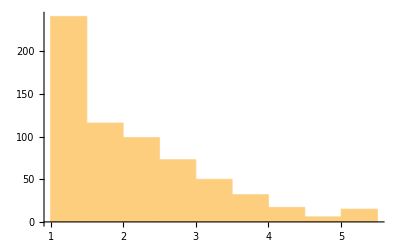

```mathematica
dataA1[Histogram,"TC"]
```

Q7: Make a simple linear regression of ‘age’ on the ‘average total alcohol consumption per week’ of each student. We call this model ‘lm’. What is the value of the parameter age in the ‘lm’ model?
Hint: “LinearModelFit” and “ParameterTable”.

```mathematica
lm=dataA1[LinearModelFit[#,age,age]&,{#age,#TC}&];
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.272438 | 0.535986 | 0.508293 | 0.611421
age | 0.0966861 | 0.031926 | 3.02845 | 0.00255599

Q8: According to the model ‘lm’, can you say that the age has a significant influence on the ‘total alcohol consumption’ of the students? Hint: Take a confidence level of 99%.

Yes, with a p Value below 0.01, age has on average, a significant and here, positive impact on the total alcohol consumption at a 99% confidence level.

Q9: What is the value of the R Squared for the model ‘lm’?
Hint: “LinearModelFit” and “AdjustedRSquared”

```mathematica
lm["RSquared"]
```

0.0139773

Q10: Using the model ‘lm’, what is the ‘average total alcohol consumption per week’ of a student who is 20 years old?
Hint: “LinearModelFit”

```mathematica
lm[20]
```

2.20616

Q11: Using the model lm, what is the confidence interval for the parameter ‘age’ at the 99% confidence level? Hint: ‘ParameterConfidenceIntervals’

```mathematica
lm["ParameterConfidenceIntervals",ConfidenceLevel->.99]
```

{{-1.11225,1.65713},{0.014207,0.179165}}

Q12: Let’s recode one of the variables to make another model later. Select the correct code that recodes the variable ‘sex’ into a variable that takes the value 0 for Male and takes the value 1 for Female. Additionally, this code should include the new dummy variable ‘sex’ in your existing dataset.

```mathematica
dataA1=dataA1/.{"M"->0,"F"->1}
```

Dataset[<>]

Q13: Let’s try to get a better model. Create a multiple regression model, called ‘lm1’, of the variables ‘sex’, ‘age’, ‘studytime’ and ‘goout’ on ‘TC’. What is the value of the parameter ‘goout’ in this model?

```mathematica
lm1=dataA1[LinearModelFit[#,{sex,age,studytime,goout},{sex,age,studytime,goout}]&,{#sex,#age,#studytime,#goout,#TC}&];
lm1[{"ParameterTable"}]//TableForm
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.353223 | 0.476532 | 0.741236 | 0.45882
sex | -0.605729 | 0.0705201 | -8.58945 | 6.57635×10^-17
age | 0.0763474 | 0.0280335 | 2.72344 | 0.00663577
studytime | -0.138339 | 0.0418377 | -3.30657 | 0.000996961
goout | 0.27766 | 0.0291222 | 9.53433 | 3.03107×10^-20

Q14: What is the value of the adjusted R squared for the multiple regression model ‘lm1’? Hint: “LinearModelFit” and “AdjustedRSquared”

```mathematica
lm1["AdjustedRSquared"]
```

0.250277

Q16: Luke: Using the model ‘lm1’, what is the predicted ‘average total alcohol consumption per week’ of a male student who is 20 years old, has a value of 1 for studytime and a value of 5 for goout? Hint: “LinearModelFit”

```mathematica
lm1[0,20,1,5]
```

3.13013